8.58

1

-4

0.2

50

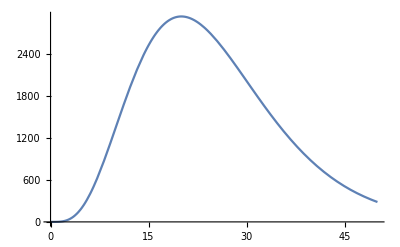

(a1 ⅇ^(-b1 p))/(b1 p)-(a2 ⅇ^(-b2 p))/(b2 p)

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a1→113649.,a2→221001.,b1→0.0772298,b2→0.10562}

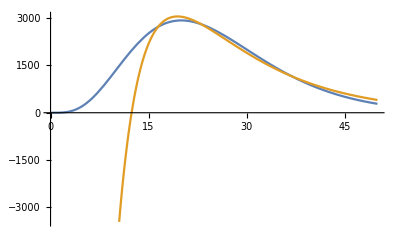

```mathematica
Clear[R0,alpha,b,p,y,a1,a2,b1,b2, alp,bet, w,t,s]

R0=8.58
a=1
alp = -4
bet = 0.2
w[p_,alpha_,b_] = Exp[-b*p]/(p/a)^(alpha);  
og = 50
                                                                      (* tempered Riesz FC *)
data = Table[{x,w[x,alp,bet]},{x,15,og,0.01}];
Plot[w[x,alp,bet],{x,0,og}]

y[ p_, a1_,a2_,b1_,b2_] =a1 *Exp[-b1*p]/(b1*p)- a2 *Exp[-b2*p]/(b2*p); 
t = a1 *Exp[-b1*p]/(b1*p)- a2 *Exp[-b2*p]/(b2*p) 
s= FindFit[data,y[p,a1,a2,b1,b2],{a1,a2,b1,b2},p,MaxIterations->1000]
Plot[{w[p,alp,bet],t /. s},{p,0, og}]
```